# Proportional Braking / Reverse Driving Transition

Robert Atkinson
7 August 2018

We compute where the proportional braking / reverse driving transition should lie

## Section. Administrivia

### Section.Subsection. Load-In

We load output we previously computed.

```mathematica
Get[NotebookDirectory[] <> "Utilities.m"]
```

```mathematica
inputDirectory = FileNameJoin[{NotebookDirectory[],"MotorPhysicsGears.Output"}] <> $PathnameSeparator
```

C:\ftc\RobotPhysics\MotorPhysicsGears.Output\

```mathematica
Get[inputDirectory <> "ParametersUnitsAndAssumptions.m"];
$Assumptions = parameterAssumptions
```

{Bafter∈ℝ,constvapp∈ℝ,constτappafter∈ℝ,Jafter∈ℝ,i[_]∈ℝ,vapp[_]∈ℝ,vg[_]∈ℝ,α[_]∈ℝ,θ[_]∈ℝ,τ[_]∈ℝ,τappafter[_]∈ℝ,ω[_]∈ℝ,Ke>0,Kt>0,L>0,R>0,η>0,Ν>0,B≥0,J≥0,t≥0}

```mathematica
Get[inputDirectory <> "MotorModels.m"];
```

```mathematica
Get[inputDirectory <> "MotorTimeDomainFunctions.m"];
```

```mathematica
Get[inputDirectory <> "SteadyState.m"];
```

```mathematica
Get[inputDirectory <> "Misc.m"];
```

## Section. Locating the Transition Point

### Section.Subsection. General

In the steady state (no acceleration), the back EMF is proportional to the steady state velocity Ω (in radians per second).

```mathematica
backEmfEqns = {ssEmf == Ke Ω}
```

{ssEmf==Ke Ω}

### Section.Subsection. Proportional Braking

We need to know the beginning and endpoints of the proportional braking curve, but here need not assume it is linear.

0% proportional braking is 100% H-bridge state 0. In that state, there is zero torque, as we have an open circuit. In order to determine the transition between proportional braking and reverse driving, rather than dealing with open circuits we will determine for each situation of relevance an equivalent instantaneous DC applied voltage for an H-bridge-less variant of the motor. For the zero-torque situation, we need to examine our voltage differential equation.

```mathematica
diffEqns[[3]]
```

R i[t]+vg[t]+L i'[t]==vapp[t]

If we’re in steady state at velocity Ω, and we instantaneously drop the voltage, to what level should we drop it so that the torque (and thus the current) as averaged over our PID loop execution interval (50ms) is zero? We haven’t yet completed that analysis, so for now we’ll use an approximation. If there is zero torque, there is zero current. Which means that drop across the resistor is zero. After a couple of time constants, the drop across the inductor will also be zero, and we’re left with:

```mathematica
diffEqns[[3]] /. {i[t] -> 0, i'[t] -> 0}
```

vg[t]==vapp[t]

That is, the voltage we should drop our applied voltage vappt[t] to is (approximately) the current back EMF. This is only approximate, as it doesn’t account for the exponential ramp down of the current, nor does it consider the deceleration of the motor (and consequent drop in the back EMF) that will happen over the PID loop interval, but it’s the best we have on hand for now.

We recall that this is happening at 0% proportional braking, which we wish to be coincident to the origin.

```mathematica
prop0Eqns = { controlProp0 == 0, voltProp0 == ssEmf }
```

{controlProp0==0,voltProp0==ssEmf}

At 100% proportional braking, we have shorted across the motor terminals; the instantaneous applied voltage is zero.

```mathematica
prop100Eqns = {voltProp100 == 0}
```

{voltProp100==0}

We define a linear curve for proportional braking, though in the below we only use it for plotting, not in the determination of the transition point.

```mathematica
voltProp[control_]  := voltProp0 + (voltProp100 - voltProp0) / (controlProp100 - controlProp0) * (control - controlProp0)
voltProp[controlProp100]
voltProp[controlProp0]
```

voltProp100

voltProp0

### Section.Subsection. Reverse Driving

0% reverse driving is almost the same as 100% proportional braking except that there’s a diode eating some of the voltage alongside the resistor and the inductor. Thus, going back to our differential equation above, the instantaneous equivalent applied voltage needs to be adjusted slightly positive to balance.

```mathematica
reverse0Eqns = { voltReverse0 == -(0 - diodeDrop) }
```

{voltReverse0==diodeDrop}

100% reverse driving applies the full negative battery voltage:

```mathematica
reverse100Eqns = { controlReverse100 == -controlMax, voltReverse100 == -batteryVoltage }
```

{controlReverse100==-controlMax,voltReverse100==-batteryVoltage}

### Section.Subsection. Continuity

We will assume linearity of reverse driving in order to set up our continuity of voltage (we only use that fact in the initial duty cycle range of reverse driving).

```mathematica
voltReverse[control_]  := voltReverse0 + (voltReverse100 - voltReverse0) / (controlReverse100 - controlReverse0) * (control - controlReverse0)
voltReverse[controlReverse100]
voltReverse[controlReverse0]
```

voltReverse100

voltReverse0

Because of the diode voltage drop, when we stitch proportional braking beside reverse driving so as to have a continuous overall voltage curve, there is necessarily a small overlap in the two curves: as we proceed from small to large control signal magnitude (remember that proportional braking and reverse driving are placed in the negative control signal range), the reverse driving curve begins before the proportional braking curve ends. That is, Abs[controlReverse0] <= Abs[controlProp100].

Here, we choose to use braking in the overlap. Thus, here our transition point is controlProp100.

```mathematica
controlTransition = controlProp100;
controlOther = controlReverse0;
```

Our continuity requirement is that at the transition, the two curves must coincide.

```mathematica
ctyEqns = { voltProp[controlTransition] == voltReverse[controlTransition] }
```

{voltProp100==voltReverse0+((controlProp100-controlReverse0) (-voltReverse0+voltReverse100))/(-controlReverse0+controlReverse100)}

### Section.Subsection. Linearity

All other things being equal, what we want is that the overall voltage vs control signal in the negative control range be as linear as possible. The shapes of the two curves, and the voltages at their endpoints is fixed; all we have to control is the transition threshold. We assume that the duty cycle response curves of both modes is linear. (While they’re not entirely so, they’re close, and we need to start somewhere. If we actually knew the curves we’d do a least squares fit.) Then, the overall concatenation can best be fit as  linear by matching the slopes of the proportional braking as a whole and the reverse driving as a whole.

```mathematica
slopeEqns = { 
slope == (voltProp100 - voltProp0) / (controlProp100 - controlProp0),
slope == (voltReverse100 - voltReverse0) / (controlReverse100 - controlReverse0)
}
```

{slope==(-voltProp0+voltProp100)/(-controlProp0+controlProp100),slope==(-voltReverse0+voltReverse100)/(-controlReverse0+controlReverse100)}

### Section.Subsection. Summary

We put all our equations together.

```mathematica
(eqns = Join[backEmfEqns, prop0Eqns, prop100Eqns, reverse0Eqns, reverse100Eqns, ctyEqns, slopeEqns]) // prettyPrint
```

ssEmf==Ke Ω
controlProp0==0
voltProp0==ssEmf
voltProp100==0
voltReverse0==diodeDrop
controlReverse100==-controlMax
voltReverse100==-batteryVoltage
voltProp100==voltReverse0+((controlProp100-controlReverse0) (voltReverse100-voltReverse0))/(controlReverse100-controlReverse0)
slope==(voltProp100-voltProp0)/(controlProp100-controlProp0)
slope==(voltReverse100-voltReverse0)/(controlReverse100-controlReverse0)

### Section.Subsection. Solving

We solve these equations.

```mathematica
solveFor = {controlTransition, controlOther, slope, voltProp0, voltProp100, voltReverse0,voltReverse100, controlProp0, controlReverse100, ssEmf};
soln = uniqueSolve[eqns, solveFor];
soln // prettyPrint
```

controlProp100→-(controlMax Ke Ω)/(batteryVoltage+Ke Ω)
controlReverse0→(controlMax diodeDrop-controlMax Ke Ω)/(batteryVoltage+Ke Ω)
slope→(batteryVoltage+Ke Ω)/controlMax
voltProp0→Ke Ω
voltProp100→0
voltReverse0→diodeDrop
voltReverse100→-batteryVoltage
controlProp0→0
controlReverse100→-controlMax
ssEmf→Ke Ω

The control transition point we seek is the following:

```mathematica
controlTransition /. soln
```

-(controlMax Ke Ω)/(batteryVoltage+Ke Ω)

## Section. Verification

### Section.Subsection. Check

Let us verify that at the control transition point, the two curves coincide.

```mathematica
voltProp[controlTransition] - voltReverse[controlTransition]
% /. soln
% // FullSimplify
```

voltProp100-voltReverse0-((controlProp100-controlReverse0) (-voltReverse0+voltReverse100))/(-controlReverse0+controlReverse100)

-diodeDrop-((-batteryVoltage-diodeDrop) (-(controlMax Ke Ω)/(batteryVoltage+Ke Ω)-(controlMax diodeDrop-controlMax Ke Ω)/(batteryVoltage+Ke Ω)))/(-controlMax-(controlMax diodeDrop-controlMax Ke Ω)/(batteryVoltage+Ke Ω))

0

### Section.Subsection. In Real Life

We examine what this looks like for an actual motor. We choose a NeveRest 60. We ignore the gearing since we want the Ke relative to the pre-gearbox armature velocity, not the post-gearbox shaft velocity.

```mathematica
aMotor = motorParameters["AM 60 A", Geared -> False] // siUnits // clearUnits
constants = {diodeDrop -> 7/10, Ke -> (Ke /. aMotor), batteryVoltage -> 12, controlMax -> 32767}
```

<|R→33/10,L→347/500000,Ke→533/500,Kt→533/500,J→1041/100000000,B→33/1000,Ν→1,η→1,Jafter→0,Bafter→0,constτappafter→0|>

{diodeDrop→7/10,Ke→533/500,batteryVoltage→12,controlMax→32767}

There are three points of relevance to us.

```mathematica
points = {
Z -> {controlProp0, voltProp0},
T -> {controlProp100, voltProp100},
R -> {controlReverse100, voltReverse100}
}
```

{Z→{controlProp0,voltProp0},T→{controlProp100,voltProp100},R→{controlReverse100,voltReverse100}}

The maximum velocity of this motor is just over 10 radians / second.

```mathematica
ssVel /. ss /. aMotor /. constvapp -> batteryVoltage /. constants // N
```

10.2726

At that velocity, what part of the negative control range is devoted to proportional braking?

{Ω→10.27}

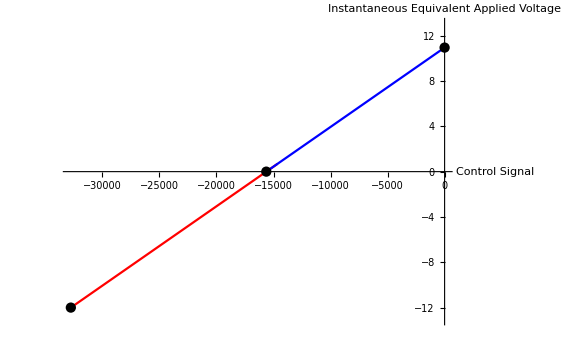

```mathematica
speed = {Ω -> 10.27}
all = Join[soln, constants, speed];
p1 = Plot[Evaluate[voltReverse[control] //. all], {control, controlReverse100, controlReverse0} //. all, PlotStyle->Red, AxesOrigin->{0,0}, PlotRange->Evaluate[{-batteryVoltage-1, batteryVoltage+1} //. all], 
AxesLabel->{HoldForm[Control Signal], HoldForm[Instantaneous Equivalent Applied Voltage]},
ImageSize->Large];
p2 = Plot[Evaluate[voltProp[control] //. all], {control, controlProp100, controlProp0} //. all, PlotStyle->Blue];
p3 = ListPlot[{Z, T, R}/. (points //. all), AxesOrigin-> {0,0}, PlotStyle->Black];
Show[p1,p2,p3]
```

Answer: about half of it. Good. It will be less for lesser velocities, but still a good chunk.

## Section. Revision History

2018.08.07 Initial version.